```mathematica
Clear["Global`"];
```

```mathematica
U={22,24,26,28,30,32,34,35};
```

```mathematica
λ={54.8,49.7,46.4,42.9,39.9,37.5,35.1,33.9};
```

```mathematica
x=(1/(U ))
```

{1/22000,1/24000,1/26000,1/28000,1/30000,1/32000,1/34000,1/35000}

```mathematica
y=λ 10^-12
```

{5.48×10^-11,4.97×10^-11,4.64×10^-11,4.29×10^-11,3.99×10^-11,3.75×10^-11,3.51×10^-11,3.39×10^-11}

```mathematica
A=(Sum[ x[[i]] y[[i]],{i,8}]-8Mean[x]Mean[y])/(Sum[x[[i]]^2,{i,8}]-8Mean[x]^2)
```

1.22162×10^-6

```mathematica
c=Mean[y]-A Mean[x]
```

-8.21564×10^-13

```mathematica
d=Sum[(x[[i]]-Mean[x])^2,{i,8}]
```

135446558431/533750702284800000000

```mathematica
dA=Sqrt[(1/(6 d))Sum[(y[[i]]-A x[[i]]-c)^2,{i,8}]]
```

1.33487×10^-8

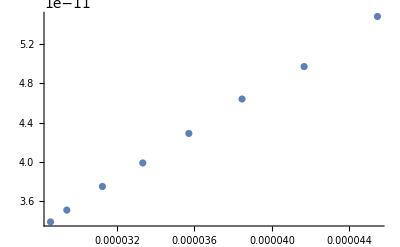

```mathematica
data=ListPlot[Table[{x[[i]],y[[i]]},{i,8}]]
```

```mathematica
speedLight=299792458
```

299792458

```mathematica
funcharge = 1.6021766208 10^-19
```

1.60218×10^-19

```mathematica
dfuncharge = 0.0000000098 10^-19
```

9.8×10^-28

```mathematica
h=1.22 10^-6 (1.60218 10^-19)/speedLight
```

6.52004×10^-34

```mathematica
dh = (funcharge/speedLight) 1 10^-8
```

5.34429×10^-36